# Hatsuda QNMs Method

Lectures on Resurgence, University of Alabama, 2020

Author: Marco Knipfer
Reproducing the paper: 1906.07232 (author: Hatsuda)

## 0) Some variables and functions

```mathematica
prec= 300;
order = 100;
tempOrder = 2 order + 2;
padeOrder = order/2;
```

## 1) Metric and Differential Equation

```mathematica
r0metric = 1;
d = 4;
l = 0;
s = 0;
n = 0;
```

```mathematica
f[r_] :=1 - (r0metric/r)^(d-3) (*+ r^2/R^2*);
Vgeneral[r_, fgeneral_] := ((d-2)(d-4))/(4 r^2)fgeneral[r] + (d-2)/(2r)(1-s^2)fgeneral'[r] + l(l+d-3)/r^2;
V[r_] :=  f[r]Vgeneral[r, f]//Simplify;
```

```mathematica
V[r] (*Regge-Wheeler potential*)
```

(-1+r)/r^4

The differential equation has the form
(ϵ^2 d^2/(dr_*)^2 + ω^2- V(r(r_*)))ϕ(r_*) = 0

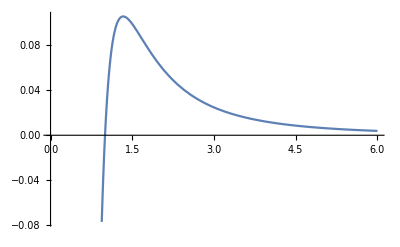

```mathematica
Plot[V[r], {r,0,6}]
```

next we would have to transform ℏ=iϵ, E=-ω^2 to invert the potential, but we do this implicitly later.

## 2) Shift so that minimum of V is at zero, expand around it

```mathematica
r0 = r/.FindRoot[D[V[r],r] == 0, {r, 1.5}, WorkingPrecision->prec];
```

```mathematica
r0//N
```

1.33333

Tortoise coordinate r_*(r)
- r_(*0) = r_*(r0)
- r = r_0+δ
- r_* = r_(*0)+ δ_*(δ)
- δ(δ_*)

This is a trick to calculate the tortoise coordinate  V(r_0+δ(δ_*)).

```mathematica
δsSeries = (Series[1/f[r0+δδ], {δδ, 0, tempOrder}, Assumptions->{δδ∈Reals}]*δδ)/.{δδ->δ};
δsSeries2 =((Normal@ δsSeries)/.{δ^nn_ -> δ^nn / nn})+ O[δ]^(tempOrder+1);
```

```mathematica
δsSeries2//N
```

4. (δ+0.)-4.5 (δ+0.)^2+9. (δ+0.)^3-20.25 (δ+0.)^4+48.6 (δ+0.)^5-121.5 (δ+0.)^6+312.429 (δ+0.)^7-820.125 (δ+0.)^8+2187. (δ+0.)^9-5904.9 (δ+0.)^10+16104.3 (δ+0.)^11-44286.8 (δ+0.)^12+122640. (δ+0.)^13-341641. (δ+0.)^14+956594. (δ+0.)^15-2.69042×10^6 (δ+0.)^16+7.59648×10^6 (δ+0.)^17-2.15234×10^7 (δ+0.)^18+6.11717×10^7 (δ+0.)^19-1.74339×10^8 (δ+0.)^20+4.98112×10^8 (δ+0.)^21-1.42641×10^9 (δ+0.)^22+4.09318×10^9 (δ+0.)^23-1.17679×10^10 (δ+0.)^24+3.38915×10^10 (δ+0.)^25-9.77641×10^10 (δ+0.)^26+2.8243×10^11 (δ+0.)^27-8.17028×10^11 (δ+0.)^28+2.36656×10^12 (δ+0.)^29-6.86304×10^12 (δ+0.)^30+1.99249×10^13 (δ+0.)^31-5.79069×10^13 (δ+0.)^32+1.68456×10^14 (δ+0.)^33-4.90505×10^14 (δ+0.)^34+1.42947×10^15 (δ+0.)^35-4.1693×10^15 (δ+0.)^36+1.21698×10^16 (δ+0.)^37-3.55487×10^16 (δ+0.)^38+1.03912×10^17 (δ+0.)^39-3.03942×10^17 (δ+0.)^40+8.89585×10^17 (δ+0.)^41-2.60521×10^18 (δ+0.)^42+7.63388×10^18 (δ+0.)^43-2.23812×10^19 (δ+0.)^44+6.56514×10^19 (δ+0.)^45-1.92673×10^20 (δ+0.)^46+5.65719×10^20 (δ+0.)^47-1.6618×10^21 (δ+0.)^48+4.88366×10^21 (δ+0.)^49-1.4358×10^22 (δ+0.)^50+4.22293×10^22 (δ+0.)^51-1.24252×10^23 (δ+0.)^52+3.65722×10^23 (δ+0.)^53-1.07685×10^24 (δ+0.)^54+3.1718×10^24 (δ+0.)^55-9.34549×10^24 (δ+0.)^56+2.75446×10^25 (δ+0.)^57-8.12091×10^25 (δ+0.)^58+2.39498×10^26 (δ+0.)^59-7.06519×10^26 (δ+0.)^60+2.08481×10^27 (δ+0.)^61-6.15356×10^27 (δ+0.)^62+1.81676×10^28 (δ+0.)^63-5.36513×10^28 (δ+0.)^64+1.58478×10^29 (δ+0.)^65-4.6823×10^29 (δ+0.)^66+1.38372×10^30 (δ+0.)^67-4.09012×10^30 (δ+0.)^68+1.20925×10^31 (δ+0.)^69-3.57594×10^31 (δ+0.)^70+1.05767×10^32 (δ+0.)^71-3.12894×10^32 (δ+0.)^72+9.25825×10^32 (δ+0.)^73-2.73994×10^33 (δ+0.)^74+8.11022×10^33 (δ+0.)^75-2.40105×10^34 (δ+0.)^76+7.10961×10^34 (δ+0.)^77-2.10554×10^35 (δ+0.)^78+6.23666×10^35 (δ+0.)^79-1.84761×10^36 (δ+0.)^80+5.4744×10^36 (δ+0.)^81-1.62229×10^37 (δ+0.)^82+4.80824×10^37 (δ+0.)^83-1.4253×10^38 (δ+0.)^84+4.22559×10^38 (δ+0.)^85-1.25294×10^39 (δ+0.)^86+3.71561×10^39 (δ+0.)^87-1.10202×10^40 (δ+0.)^88+3.2689×10^40 (δ+0.)^89-9.69774×10^40 (δ+0.)^90+2.87735×10^41 (δ+0.)^91-8.53823×10^41 (δ+0.)^92+2.53392×10^42 (δ+0.)^93-7.5209×10^42 (δ+0.)^94+2.23252×10^43 (δ+0.)^95-6.6278×10^43 (δ+0.)^96+1.96784×10^44 (δ+0.)^97-5.84328×10^44 (δ+0.)^98+1.73528×10^45 (δ+0.)^99-5.15378×10^45 (δ+0.)^100+1.53082×10^46 (δ+0.)^101-4.54745×10^46 (δ+0.)^102+1.35099×10^47 (δ+0.)^103-4.014×10^47 (δ+0.)^104+1.19273×10^48 (δ+0.)^105-3.54444×10^48 (δ+0.)^106+1.05339×10^49 (δ+0.)^107-3.13092×10^49 (δ+0.)^108+9.30658×10^49 (δ+0.)^109-2.76659×10^50 (δ+0.)^110+8.22501×10^50 (δ+0.)^111-2.44547×10^51 (δ+0.)^112+7.27149×10^51 (δ+0.)^113-2.16231×10^52 (δ+0.)^114+6.43053×10^52 (δ+0.)^115-1.91253×10^53 (δ+0.)^116+5.68854×10^53 (δ+0.)^117-1.6921×10^54 (δ+0.)^118+5.03364×10^54 (δ+0.)^119-1.49751×10^55 (δ+0.)^120+4.4554×10^55 (δ+0.)^121-1.32566×10^56 (δ+0.)^122+3.94466×10^56 (δ+0.)^123-1.17385×10^57 (δ+0.)^124+3.49339×10^57 (δ+0.)^125-1.0397×10^58 (δ+0.)^126+3.09454×10^58 (δ+0.)^127-9.21108×10^58 (δ+0.)^128+2.7419×10^59 (δ+0.)^129-8.16244×10^59 (δ+0.)^130+2.43004×10^60 (δ+0.)^131-7.23489×10^60 (δ+0.)^132+2.15415×10^61 (δ+0.)^133-6.41421×10^61 (δ+0.)^134+1.91001×10^62 (δ+0.)^135-5.6879×10^62 (δ+0.)^136+1.69391×10^63 (δ+0.)^137-5.04492×10^63 (δ+0.)^138+1.50259×10^64 (δ+0.)^139-4.47556×10^64 (δ+0.)^140+1.33315×10^65 (δ+0.)^141-3.97127×10^65 (δ+0.)^142+1.18305×10^66 (δ+0.)^143-3.52451×10^66 (δ+0.)^144+1.05006×10^67 (δ+0.)^145-3.1286×10^67 (δ+0.)^146+9.32196×10^67 (δ+0.)^147-2.77769×10^68 (δ+0.)^148+8.27715×10^68 (δ+0.)^149-2.46659×10^69 (δ+0.)^150+7.35076×10^69 (δ+0.)^151-2.19072×10^70 (δ+0.)^152+6.52921×10^70 (δ+0.)^153-1.94604×10^71 (δ+0.)^154+5.80046×10^71 (δ+0.)^155-1.72898×10^72 (δ+0.)^156+5.15392×10^72 (δ+0.)^157-1.53639×10^73 (δ+0.)^158+4.58018×10^73 (δ+0.)^159-1.36547×10^74 (δ+0.)^160+4.07095×10^74 (δ+0.)^161-1.21375×10^75 (δ+0.)^162+3.6189×10^75 (δ+0.)^163-1.07905×10^76 (δ+0.)^164+3.21753×10^76 (δ+0.)^165-9.59445×10^76 (δ+0.)^166+2.8611×10^77 (δ+0.)^167-8.53221×10^77 (δ+0.)^168+2.54452×10^78 (δ+0.)^169-7.58865×10^78 (δ+0.)^170+2.26328×10^79 (δ+0.)^171-6.75037×10^79 (δ+0.)^172+2.0134×10^80 (δ+0.)^173-6.0055×10^80 (δ+0.)^174+1.79135×10^81 (δ+0.)^175-5.34353×10^81 (δ+0.)^176+1.594×10^82 (δ+0.)^177-4.75514×10^82 (δ+0.)^178+1.41857×10^83 (δ+0.)^179-4.23207×10^83 (δ+0.)^180+1.26261×10^84 (δ+0.)^181-3.76701×10^84 (δ+0.)^182+1.12393×10^85 (δ+0.)^183-3.35346×10^85 (δ+0.)^184+1.0006×10^86 (δ+0.)^185-2.98566×10^86 (δ+0.)^186+8.90908×10^86 (δ+0.)^187-2.65851×10^87 (δ+0.)^188+7.93333×10^87 (δ+0.)^189-2.36747×10^88 (δ+0.)^190+7.06523×10^88 (δ+0.)^191-2.10853×10^89 (δ+0.)^192+6.29281×10^89 (δ+0.)^193-1.87811×10^90 (δ+0.)^194+5.60544×10^90 (δ+0.)^195-1.67305×10^91 (δ+0.)^196+4.99368×10^91 (δ+0.)^197-1.49054×10^92 (δ+0.)^198+4.44915×10^92 (δ+0.)^199-1.32807×10^93 (δ+0.)^200+3.96439×10^93 (δ+0.)^201-1.18343×10^94 (δ+0.)^202+O[δ+0.]^203

```mathematica
δSeries =Normal@InverseSeries[δsSeries2, δs];
```

```mathematica
δSeries//N
```

0.25 δs+0.0703125 δs^2+0.00439453 δs^3-0.00185394 δs^4-0.00016222 δs^5+0.000100663 δs^6+6.57596×10^-6 δs^7-6.67917×10^-6 δs^8-2.08369×10^-7 δs^9+4.84089×10^-7 δs^10-3.3678×10^-9 δs^11-3.67073×10^-8 δs^12+1.74817×10^-9 δs^13+2.84851×10^-9 δs^14-2.59988×10^-10 δs^15-2.23114×10^-10 δs^16+3.11002×10^-11 δs^17+1.74573×10^-11 δs^18-3.39592×10^-12 δs^19-1.35154×10^-12 δs^20+3.5261×10^-13 δs^21+1.02421×10^-13 δs^22-3.54345×10^-14 δs^23-7.48379×10^-15 δs^24+3.47652×10^-15 δs^25+5.1391×10^-16 δs^26-3.34544×10^-16 δs^27-3.13865×10^-17 δs^28+3.16513×10^-17 δs^29+1.43317×10^-18 δs^30-2.94718×10^-18 δs^31+1.3588×10^-21 δs^32+2.70096×10^-19 δs^33-1.22935×10^-20 δs^34-2.43434×10^-20 δs^35+2.23615×10^-21 δs^36+2.15405×10^-21 δs^37-3.05229×10^-22 δs^38-1.86603×10^-22 δs^39+3.69359×10^-23 δs^40+1.57551×10^-23 δs^41-4.1743×10^-24 δs^42-1.28718×10^-24 δs^43+4.50766×10^-25 δs^44+1.00525×10^-25 δs^45-4.70633×10^-26 δs^46-7.3343×10^-27 δs^47+4.78265×10^-27 δs^48+4.75035×10^-28 δs^49-4.74881×10^-28 δs^50-2.3293×10^-29 δs^51+4.61692×10^-29 δs^52+9.56457×10^-32 δs^53-4.39905×10^-30 δs^54+1.93029×10^-31 δs^55+4.10725×10^-31 δs^56-3.73238×10^-32 δs^57-3.75347×10^-32 δs^58+5.29861×10^-33 δs^59+3.3495×10^-33 δs^60-6.62106×10^-34 δs^61-2.90695×10^-34 δs^62+7.6958×10^-35 δs^63+2.43707×10^-35 δs^64-8.52275×10^-36 δs^65-1.95073×10^-36 δs^66+9.10557×10^-37 δs^67+1.45827×10^-37 δs^68-9.45138×10^-38 δs^69-9.69447×10^-39 δs^70+9.57059×10^-39 δs^71+4.933×10^-40 δs^72-9.47659×10^-40 δs^73-3.80998×10^-42 δs^74+9.18542×10^-41 δs^75-3.88743×10^-42 δs^76-8.71547×10^-42 δs^77+7.80741×10^-43 δs^78+8.08706×10^-43 δs^79-1.13238×10^-43 δs^80-7.32212×10^-44 δs^81+1.43917×10^-44 δs^82+6.44372×10^-45 δs^83-1.69763×10^-45 δs^84-5.47569×10^-46 δs^85+1.90537×10^-46 δs^86+4.44224×10^-47 δs^87-2.06099×10^-47 δs^88-3.3675×10^-48 δs^89+2.16415×10^-48 δs^90+2.27516×10^-49 δs^91-2.21546×10^-49 δs^92-1.18809×10^-50 δs^93+2.21649×10^-50 δs^94+1.27967×10^-52 δs^95-2.16965×10^-51 δs^96+8.85022×10^-53 δs^97+2.07814×10^-52 δs^98-1.83249×10^-53 δs^99-1.9459×10^-53 δs^100+2.6981×10^-54 δs^101+1.77743×10^-54 δs^102-3.46777×10^-55 δs^103-1.57777×10^-55 δs^104+4.12986×10^-56 δs^105+1.35233×10^-56 δs^106-4.67527×10^-57 δs^107-1.10683×10^-57 δs^108+5.09755×10^-58 δs^109+8.47118×10^-59 δs^110-5.39286×10^-59 δs^111-5.79138×10^-60 δs^112+5.56004×10^-60 δs^113+3.08749×10^-61 δs^114-5.60048×10^-61 δs^115-4.16551×10^-63 δs^116+5.51802×10^-62 δs^117-2.16712×10^-63 δs^118-5.31882×10^-63 δs^119+4.61283×10^-64 δs^120+5.01114×10^-64 δs^121-6.87432×10^-65 δs^122-4.60513×10^-65 δs^123+8.91061×10^-66 δs^124+4.1126×10^-66 δs^125-1.06865×10^-66 δs^126-3.54671×10^-67 δs^127+1.21733×10^-67 δs^128+2.92169×10^-68 δs^129-1.33488×10^-68 δs^130-2.25252×10^-69 δs^131+1.41981×10^-69 δs^132+1.55464×10^-70 δs^133-1.47131×10^-70 δs^134-8.43623×10^-72 δs^135+1.48929×10^-71 δs^136+1.34854×10^-73 δs^137-1.47433×10^-72 δs^138+5.56758×10^-74 δs^139+1.42769×10^-73 δs^140-1.21706×10^-74 δs^141-1.35123×10^-74 δs^142+1.83293×10^-75 δs^143+1.24739×10^-75 δs^144-2.39251×10^-76 δs^145-1.11908×10^-76 δs^146+2.88538×10^-77 δs^147+9.69679×10^-78 δs^148-3.3028×10^-78 δs^149-8.02891×10^-79 δs^150+3.63779×10^-79 δs^151+6.22697×10^-80 δs^152-3.88523×10^-80 δs^153-4.33263×10^-81 δs^154+4.04198×10^-81 δs^155+2.38847×10^-82 δs^156-4.10683×10^-82 δs^157-4.37144×10^-84 δs^158+4.08051×10^-83 δs^159-1.47952×10^-84 δs^160-3.96565×10^-84 δs^161+3.32132×10^-85 δs^162+3.76667×10^-85 δs^163-5.0505×10^-86 δs^164-3.48966×10^-86 δs^165+6.63248×10^-87 δs^166+3.1422×10^-87 δs^167-8.03645×10^-88 δs^168-2.73321×10^-88 δs^169+9.23598×10^-89 δs^170+2.27272×10^-89 δs^171-1.02095×10^-89 δs^172-1.77164×10^-90 δs^173+1.09405×10^-90 δs^174+1.24153×10^-91 δs^175-1.1418×10^-91 δs^176-6.94342×10^-93 δs^177+1.16366×10^-92 δs^178+1.42157×10^-94 δs^179-1.15964×10^-93 δs^180+4.03046×10^-95 δs^181+1.1303×10^-94 δs^182-9.29653×10^-96 δs^183-1.07672×10^-95 δs^184+1.42665×10^-96 δs^185+1.00049×10^-96 δs^186-1.88383×10^-97 δs^187-9.03627×10^-98 δs^188+2.29202×10^-98 δs^189+7.88579×10^-99 δs^190-2.64321×10^-99 δs^191-6.58126×10^-100 δs^192+2.93077×10^-100 δs^193+5.15336×10^-101 δs^194-3.14949×10^-101 δs^195-3.6349×10^-102 δs^196+3.29572×10^-102 δs^197+2.06012×10^-103 δs^198-3.36743×10^-103 δs^199-4.63931×10^-105 δs^200+3.36418×10^-104 δs^201-1.1188×10^-105 δs^202

```mathematica
VSeries=Series[-V[r0+δSeries],{δs,0,tempOrder}]//Normal; 
v[k_]:=Coefficient[VSeries,δs,k];
```

```mathematica
VSeries//N
```

-0.105469+0.0222473 δs^2-0.00139046 δs^3-0.00332406 δs^4+0.000403287 δs^5+0.00042368 δs^6-0.000077206 δs^7-0.0000488707 δs^8+0.0000122512 δs^9+5.21428×10^-6 δs^10-1.74081×10^-6 δs^11-5.16941×10^-7 δs^12+2.29518×10^-7 δs^13+4.71618×10^-8 δs^14-2.86204×10^-8 δs^15-3.83285×10^-9 δs^16+3.41357×10^-9 δs^17+2.51364×10^-10 δs^18-3.92106×10^-10 δs^19-7.69582×10^-12 δs^20+4.35585×10^-11 δs^21-1.37103×10^-12 δs^22-4.69021×10^-12 δs^23+3.86285×10^-13 δs^24+4.89841×10^-13 δs^25-6.64419×10^-14 δs^26-4.95759×10^-14 δs^27+9.63833×10^-15 δs^28+4.84873×10^-15 δs^29-1.27553×10^-15 δs^30-4.55743×10^-16 δs^31+1.58942×10^-16 δs^32+4.07467×10^-17 δs^33-1.89459×10^-17 δs^34-3.39734×10^-18 δs^35+2.17962×10^-18 δs^36+2.52871×10^-19 δs^37-2.43292×10^-19 δs^38-1.47862×10^-20 δs^39+2.6431×10^-20 δs^40+2.63611×10^-22 δs^41-2.79932×10^-21 δs^42+1.09331×10^-22 δs^43+2.89169×10^-22 δs^44-2.56294×10^-23 δs^45-2.91159×10^-23 δs^46+4.1105×10^-24 δs^47+2.85204×10^-24 δs^48-5.69631×10^-25 δs^49-2.70801×10^-25 δs^50+7.27676×10^-26 δs^51+2.47662×10^-26 δs^52-8.80536×10^-27 δs^53-2.15745×10^-27 δs^54+1.0234×10^-27 δs^55+1.75259×10^-28 δs^56-1.15141×10^-28 δs^57-1.26678×10^-29 δs^58+1.25984×10^-29 δs^59+7.07425×10^-31 δs^60-1.34419×10^-30 δs^61-8.44806×10^-33 δs^62+1.40035×10^-31 δs^63-5.89635×10^-33 δs^64-1.42476×10^-32 δs^65+1.30028×10^-33 δs^66+1.41449×10^-33 δs^67-2.03089×10^-34 δs^68-1.36743×10^-34 δs^69+2.76331×10^-35 δs^70+1.2823×10^-35 δs^71-3.47821×10^-36 δs^72-1.1588×10^-36 δs^73+4.1556×10^-37 δs^74+9.97673×10^-38 δs^75-4.77529×10^-38 δs^76-8.00683×10^-39 δs^77+5.31743×10^-39 δs^78+5.70673×10^-40 δs^79-5.76312×10^-40 δs^80-3.11522×10^-41 δs^81+6.09491×10^-41 δs^82+2.81035×10^-43 δs^83-6.29735×10^-42 δs^84+2.73801×10^-43 δs^85+6.35754×10^-43 δs^86-5.87603×10^-44 δs^87-6.26556×10^-44 δs^88+9.06045×10^-45 δs^89+6.01489×10^-45 δs^90-1.22135×10^-45 δs^91-5.60277×10^-46 δs^92+1.52542×10^-46 δs^93+5.03044×10^-47 δs^94-1.81×10^-47 δs^95-4.30332×10^-48 δs^96+2.0669×10^-48 δs^97+3.43105×10^-49 δs^98-2.28823×10^-49 δs^99-2.42744×10^-50 δs^100+2.46658×10^-50 δs^101+1.31036×10^-51 δs^102-2.59526×10^-51 δs^103-1.01422×10^-53 δs^104+2.66849×10^-52 δs^105-1.17436×10^-53 δs^106-2.68161×10^-53 δs^107+2.48909×10^-54 δs^108+2.63123×10^-54 δs^109-3.81249×10^-55 δs^110-2.51536×10^-55 δs^111+5.11267×10^-56 δs^112+2.33359×10^-56 δs^113-6.35674×10^-57 δs^114-2.08708×10^-57 δs^115+7.51166×10^-58 δs^116+1.77868×10^-58 δs^117-8.54507×10^-59 δs^118-1.41289×10^-59 δs^119+9.42609×10^-60 δs^120+9.95822×10^-61 δs^121-1.01262×10^-60 δs^122-5.3515×10^-62 δs^123+1.06199×10^-61 δs^124+3.99493×10^-64 δs^125-1.08858×10^-62 δs^126+4.79447×10^-64 δs^127+1.0907×10^-63 δs^128-1.01166×10^-64 δs^129-1.06718×10^-64 δs^130+1.54448×10^-65 δs^131+1.01744×10^-65 δs^132-2.06517×10^-66 δs^133-9.4149×10^-67 δs^134+2.56074×10^-67 δs^135+8.39989×10^-68 δs^136-3.01821×10^-68 δs^137-7.14243×10^-69 δs^138+3.42503×10^-69 δs^139+5.66196×10^-70 δs^140-3.76928×10^-70 δs^141-3.98417×10^-71 δs^142+4.04011×10^-71 δs^143+2.14054×10^-72 δs^144-4.22794×10^-72 δs^145-1.67863×10^-74 δs^146+4.32482×10^-73 δs^147-1.89245×10^-74 δs^148-4.32464×10^-74 δs^149+3.99519×10^-75 δs^150+4.2234×10^-75 δs^151-6.09233×10^-76 δs^152-4.01933×10^-76 δs^153+8.13401×10^-77 δs^154+3.71305×10^-77 δs^155-1.00697×10^-77 δs^156-3.30768×10^-78 δs^157+1.18495×10^-78 δs^158+2.80879×10^-79 δs^159-1.34251×10^-79 δs^160-2.22441×10^-80 δs^161+1.47513×10^-80 δs^162+1.56494×10^-81 δs^163-1.57871×10^-81 δs^164-8.42938×10^-83 δs^165+1.64966×10^-82 δs^166+7.29451×10^-85 δs^167-1.68506×10^-83 δs^168+7.28806×10^-85 δs^169+1.68271×10^-84 δs^170-1.54471×10^-85 δs^171-1.6412×10^-85 δs^172+2.35618×10^-86 δs^173+1.56002×10^-86 δs^174-3.14402×10^-87 δs^175-1.43957×10^-87 δs^176+3.88888×10^-88 δs^177+1.28121×10^-88 δs^178-4.57173×10^-89 δs^179-1.08721×10^-89 δs^180+5.17427×10^-90 δs^181+8.60796×10^-91 δs^182-5.67947×10^-91 δs^183-6.06061×10^-92 δs^184+6.07193×10^-92 δs^185+3.27915×10^-93 δs^186-6.3384×10^-93 δs^187-3.19988×10^-95 δs^188+6.46806×10^-94 δs^189-2.75431×10^-95 δs^190-6.45297×10^-95 δs^191+5.87622×10^-96 δs^192+6.28828×10^-96 δs^193-8.97472×10^-97 δs^194-5.9725×10^-97 δs^195+1.19768×10^-97 δs^196+5.50762×10^-98 δs^197-1.48093×10^-98 δs^198-4.8992×10^-99 δs^199+1.74003×10^-99 δs^200+4.15634×10^-100 δs^201-1.96812×10^-100 δs^202

```mathematica
-V[r0] //N
```

-0.105469

## 3) Bender-Wu -> Get eigenvalues for energy

```mathematica
Needs["BenderWu`"]
```

```mathematica
BW=BenderWu[1/2 Sum[v[k] x^k,{k,2,2order+2}],x,n,order];
ϵpert=BWProcess[BW,OutputStyle->"Series",Coupling->Sqrt[ℏ]];
```

```mathematica
ϵpert//N
```

0.0745777-0.057373 ℏ+0.0263578 ℏ^2-0.00446658 ℏ^3-0.00367241 ℏ^4+0.00425018 ℏ^5-0.00220275 ℏ^6-0.00280889 ℏ^7+0.0117786 ℏ^8-0.0144131 ℏ^9-0.0284201 ℏ^10+0.167203 ℏ^11-0.217812 ℏ^12-1.06073 ℏ^13+6.1011 ℏ^14-5.99975 ℏ^15-80.1495 ℏ^16+439.164 ℏ^17-117.717 ℏ^18-10403.2 ℏ^19+53444.8 ℏ^20+51735.8 ℏ^21-2.11623×10^6 ℏ^22+9.90423×10^6 ℏ^23+2.98474×10^7 ℏ^24-6.32349×10^8 ℏ^25+2.56618×10^9 ℏ^26+1.67667×10^10 ℏ^27-2.64088×10^11 ℏ^28+8.48515×10^11 ℏ^29+1.13599×10^13 ℏ^30-1.4806×10^14 ℏ^31+3.05471×10^14 ℏ^32+9.59232×10^15 ℏ^33-1.07672×10^17 ℏ^34+5.18346×10^16 ℏ^35+1.00856×10^19 ℏ^36-9.84408×10^19 ℏ^37-1.72271×10^20 ℏ^38+1.30709×10^22 ℏ^39-1.09675×10^23 ℏ^40-5.53186×10^23 ℏ^41+2.06137×10^25 ℏ^42-1.43614×10^26 ℏ^43-1.47869×10^27 ℏ^44+3.90266×10^28 ℏ^45-2.09544×10^29 ℏ^46-4.16987×10^30 ℏ^47+8.74853×10^31 ℏ^48-3.03532×10^32 ℏ^49-1.30942×10^34 ℏ^50+2.28945×10^35 ℏ^51-2.5068×10^35 ℏ^52-4.65233×10^37 ℏ^53+6.88829×10^38 ℏ^54+1.39667×10^39 ℏ^55-1.87631×10^41 ℏ^56+2.34025×10^42 ℏ^57+1.49585×10^43 ℏ^58-8.57201×10^44 ℏ^59+8.76289×10^45 ℏ^60+1.14164×10^47 ℏ^61-4.41521×10^48 ℏ^62+3.47452×10^49 ℏ^63+8.53118×10^50 ℏ^64-2.54765×10^52 ℏ^65+1.33412×10^53 ℏ^66+6.7018×10^54 ℏ^67-1.63397×10^56 ℏ^68+3.44824×10^56 ℏ^69+5.67174×10^58 ℏ^70-1.15358×10^60 ℏ^71-2.10717×10^60 ℏ^72+5.21852×10^62 ℏ^73-8.85165×10^63 ℏ^74-6.30469×10^64 ℏ^75+5.23341×10^66 ℏ^76-7.24553×10^67 ℏ^77-1.078×10^69 ℏ^78+5.71531×10^70 ℏ^79-6.12717×10^71 ℏ^80-1.7005×10^73 ℏ^81+6.77613×10^74 ℏ^82-4.98807×10^75 ℏ^83-2.71268×10^77 ℏ^84+8.67955×10^78 ℏ^85-3.04867×10^79 ℏ^86-4.51776×10^81 ℏ^87+1.19288×10^83 ℏ^88+1.40658×10^83 ℏ^89-7.95938×10^85 ℏ^90+1.74182×10^87 ℏ^91+1.27124×10^88 ℏ^92-1.49142×10^90 ℏ^93+2.6616×10^91 ℏ^94+4.25161×10^92 ℏ^95-2.9763×10^94 ℏ^96+4.14501×10^95 ℏ^97+1.23554×10^97 ℏ^98-6.31851×10^98 ℏ^99+6.21666×10^99 ℏ^100

```mathematica
ϵpertCoeff := CoefficientList[ϵpert, ℏ];
```

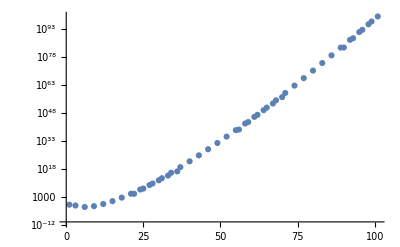

```mathematica
ListLogPlot[ϵpertCoeff]
```

```mathematica
ϵPertTrunc[h_, nmax_] := Normal[Series[ϵpert, {ℏ, 0, nmax}]]/.{ℏ->h}
```

```mathematica
ϵPertTrunc[1, 10]
```

0.003607398811381603266436078323654034748127935514920627395318435134741810614873508595696839056552251261432181036755660013168615125118369873509966779794047181575126667442635425052

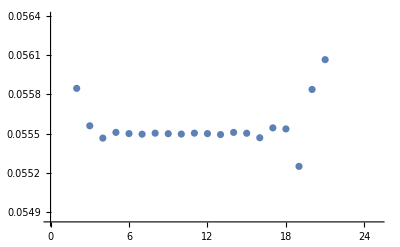

```mathematica
ListPlot[Table[ϵPertTrunc[0.4, nn], {nn,1,25}]]
```

## 4) Borel-Pade-Laplace transform

Setting ℏ=i directly during the numerical Laplace transform

```mathematica
BorelTransform[ϵpert_, ℏ_] := ϵpert/.{ℏ^nn_ -> ℏ^nn/nn!};
BorelPadeTransform[ϵpert_, ζ_,Padeorder_]:=PadeApproximant[BorelTransform[ϵpert, ℏ]/.{ℏ->ζζ}, {ζζ, 0, Padeorder}]/.{ζζ->ζ};
LaplaceTrafo[ϵpertBPT_] := NIntegrate[Exp[-t]ϵpertBPT/.ζ->I t,{t,0,∞},WorkingPrecision->prec,MaxRecursion->50];
```

```mathematica
ϵpertBPT = BorelPadeTransform[ϵpert, ζ, padeOrder];ϵBPLT = LaplaceTrafo[ϵpertBPT]; (*Borel-Pade-Laplace-transformed*)
```

NIntegrate::precw: The precision of the argument function ((ⅇ^-t («233»+0.211929510242015439365901140592713048652644303106574451953096139977312513211139866 ⅈ t-«115» t^2-«116» ⅈ t^3+«115» t^4+«61»+«103» t^46+«102» ⅈ t^47+«101» t^48+«99» ⅈ t^49+«1»))/(1+«73»+«1»)) is less than WorkingPrecision (300.).

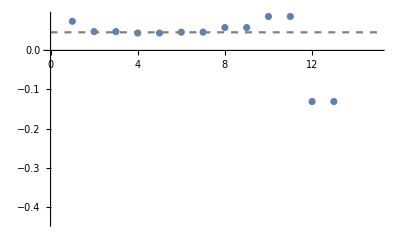

```mathematica
rePlot = ListPlot[Re@Table[ϵPertTrunc[I, nn], {nn,1,15}]];
reBPLT = Plot[Re@ϵBPLT, {nn,0,15}, PlotStyle->{Gray, Dashed}];
Show[rePlot, reBPLT]
```

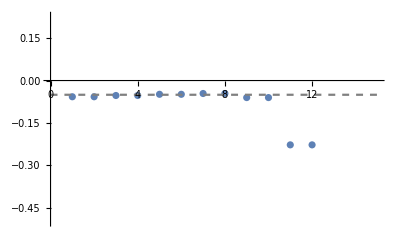

```mathematica
imPlot = ListPlot[Im@Table[ϵPertTrunc[I, nn], {nn,1,15}]];
imBPLT = Plot[Im@ϵBPLT, {nn,0,15}, PlotStyle->{Gray, Dashed}];
Show[imPlot, imBPLT]
```

```mathematica
ϵBPLT
```

0.04634329923493218346899362234928069014392172407419810030698779484412802956138773327780654813909029380084081129592973771572598406898580913206900403609139815677979993890782398549734347204403358144729104582679220208042882371651542742497741286190071533825019465743792800875984475142651646782234355787261-0.0503390557770738800336480391544907354081806007461778412172369787396636296268263145195846962198490612378135911696319811982732503338692641094430381145374053935078556027874108459618639860421708612251159960747363242506174788530241655988836538103723164919671316485204262327219849363069772653634962735923604 ⅈ

## 5) Transform back to ω

```mathematica
ω[ϵBPLT_] := Sqrt[-(v[0] + 2 I ϵBPLT)];
PolesTable[ϵpertBPT_] := ζ/.Solve[NumeratorDenominator[ϵpertBPT][[2]]==0, ζ];
```

```mathematica
ω[ϵBPLT]//N
```

0.220908-0.209785 ⅈ

## Additional: Poles in the Borel Plane

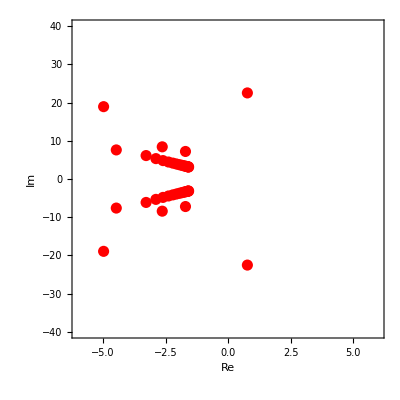

```mathematica
polesTable = PolesTable[ϵpertBPT];
ListPlot[{Re[#],Im[#]}&/@(Flatten@polesTable),AxesOrigin->{0,0},ImagePadding->50,AspectRatio->1,Frame->True,FrameLabel->{{Im,None},{Re,"complex plane"}},PlotStyle->Directive[Red,PointSize[.02]],
PlotRange->{{-6, 6},{-40, 40}}]
```

## Additional: Different Θ

```mathematica
LateralLaplaceTrafo[ϵpertBPT_,g_, Θ_] := NIntegrate[Exp[I Θ] Exp[-t Exp[I Θ]]ϵpertBPT/.{ζ->g t Exp[I Θ]},{t,0,∞},WorkingPrecision->prec,MaxRecursion->50];
```

```mathematica
LateralLaplaceTrafo[ϵpertBPT, I, 0.1]
```

NIntegrate::precw: The precision of the argument function (((0.995004+0.0998334 ⅈ) ⅇ^((-0.995004-0.0998334 ⅈ) t) («75»+(1.42432×10^-41+2.70399×10^-42 ⅈ) t^49+«1»))/(1-(0.360502-3.59299 ⅈ) t-(6.91857+1.40246 ⅈ) t^2+«67»+(1.813×10^-41-2.06407×10^-40 ⅈ) t^48+(3.07274×10^-42+5.83341×10^-43 ⅈ) t^49+«1»)) is less than WorkingPrecision (300.).

```mathematica
thetaTable = Table[{Θ, LateralLaplaceTrafo[ϵpertBPT, I, Θ]}, {Θ, 0.1, 2 Pi-0.1, 0.1}];
```

NIntegrate::precw: The precision of the argument function (((0.995004+0.0998334 ⅈ) ⅇ^((-0.995004-0.0998334 ⅈ) t) («75»+(1.42432×10^-41+2.70399×10^-42 ⅈ) t^49+«1»))/(1-(0.360502-3.59299 ⅈ) t-(6.91857+1.40246 ⅈ) t^2+«67»+(1.813×10^-41-2.06407×10^-40 ⅈ) t^48+(3.07274×10^-42+5.83341×10^-43 ⅈ) t^49+«1»)) is less than WorkingPrecision (300.).

NIntegrate::precw: The precision of the argument function (((0.980067+0.198669 ⅈ) ⅇ^(«1»«1»«1») («233»-(0.0421039-0.207705 ⅈ) t-(0.306223+0.129469 ⅈ) t^2+«69»+(5.31308×10^-42-1.3489×10^-41 ⅈ) t^49+«1»))/(1-(0.717402-3.53905 ⅈ) t-(6.50203+2.74902 ⅈ) t^2+«69»+(1.14621×10^-42-2.91002×10^-42 ⅈ) t^49+«1»)) is less than WorkingPrecision (300.).

NIntegrate::precw: The precision of the argument function (((0.955336+0.29552 ⅈ) ⅇ^((-0.955336-«19» ⅈ) t) («233»-(0.0626295-0.202464 ⅈ) t-(0.274398+0.187725 ⅈ) t^2+«73»+«1»))/(1-(1.06713-3.44975 ⅈ) t-(5.82628+3.98597 ⅈ) t^2+«71»+«1»)) is less than WorkingPrecision (300.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 50 recursive bisections in t near {t} = {5.36870655000122070254292366842094973518861046380497750998615742389801793192962077635728056083652456449291015009396071721996439935474426520144214561360091514543764808766933075459921140708379407701774739372854531834348757577534877045213200944327857814856617519084206064125984131820615853969643607309529×10^8}. NIntegrate obtained -2.67092258146082834206961257426188818435491273477129113504566564887097993659982339621457510766993082327584555075919903197023552635946773927002834037866496159356055834075794236120197284664465759347608478524349386135756797267779674365848058411595696669884455914327445427374299944359437311387461881927508`300.*^976018945044181+«322» ⅈ and -2.67092258146082834206961257426188818435491273477129113504566564887097993659982339621457510766993082327584555075919903197023552635946773927002834037866496159356055834075794236120197284664465759347608478524349386135756797267779674365848058411595696669884455914327445427374299944359437311387461881927508`300.*^976018945044181+«322» ⅈ for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.33519021794965057060602715328669512072808362921819115571525856608288125048488867071418418007465467265145838763434276136249813707745786140745408298990003548648878464090434428846370004649259371429328570490137360605663314203094777910286118360504725987719028964069314797083511448333705508212851273793193`300.*^1076684286985053-«324» ⅈ and 1.33519021794965057060602715328669512072808362921819115571525856608288125048488867071418418007465467265145838763434276136249813707745786140745408298990003548648878464090434428846370004649259371429328570490137360605663314203094777910286118360504725987719028964069314797083511448333705508212851273793193`300.*^1076684286985053-«324» ⅈ for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.85506220973495245746801072033922186089727179612192506771142704548889175097471020765152829466467400724852698078590295767093157458966334163198455920541086804356804101735783043836922500040984166176880253435448156627757415391726663176378914712587133590879646576825416368949977457481528887490345180727897`300.*^949302982109005+«322» ⅈ and 9.85506220973495245746801072033922186089727179612192506771142704548889175097471020765152829466467400724852698078590295767093157458966334163198455920541086804356804101735783043836922500040984166176880253435448156627757415391726663176378914712587133590879646576825416368949977457481528887490345180727897`300.*^949302982109005+«322» ⅈ for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.08582746300570193946713375349070421666566601758654579245555219319033867646292596779853843884469164051426068804576769404476943584359773782262756407448111681282909633223008757582946944617917386307763520087462799742692877454741300733813644597573097412863175481290627698222465188256180412070927060788511`300.*^1350778699126096+«324» ⅈ and 6.08582746300570193946713375349070421666566601758654579245555219319033867646292596779853843884469164051426068804576769404476943584359773782262756407448111681282909633223008757582946944617917386307763520087462799742692877454741300733813644597573097412863175481290627698222465188256180412070927060788511`300.*^1350778699126096+«324» ⅈ for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 50 recursive bisections in t near {t} = {1.07374079900097656156867831356209415236077083514133916727145455221695688537894689660368289596281436651767109139338360463752304313369452124164462886368859892978770276288722716595919994430547303631492966181787317478830834550061654985756887667763073193480307120983962074315953907056897109129801626394628×10^9}. NIntegrate obtained 9.33340888252466735494929962134062219267499216848693237030609555151325212475569671590361946726960916758136188663081794601909147318820140757147272163274919095952365641300645454130427523469741970167416008029119889690091232825619148896781450206977587928106186984802421518018205098550712225974323047906139`300.*^828203291738381-«323» ⅈ and 9.33340888252466735494929962134062219267499216848693237030609555151325212475569671590361946726960916758136188663081794601909147318820140757147272163274919095952365641300645454130427523469741970167416008029119889690091232825619148896781450206977587928106186984802421518018205098550712225974323047906139`300.*^828203291738381-«323» ⅈ for the integral and error estimates.

```mathematica
ExtractRe[table_] := table/.{{a_, b_} -> {a, Re[b]}};
ExtractIm[table_] := table/.{{a_, b_} -> {a, Im[b]}};
```

```mathematica
thetaTable//N
```

{{0.1,0.0463433-0.0503391 ⅈ},{0.2,0.0463433-0.0503391 ⅈ},{0.3,0.0463692-0.0503521 ⅈ},{0.4,0.0515842-0.0486974 ⅈ},{0.5,0.0534078-0.0488272 ⅈ},{0.6,0.0251225-0.0496673 ⅈ},{0.7,0.0171615-0.0486505 ⅈ},{0.8,0.0171615-0.0486505 ⅈ},{0.9,0.0171615-0.0486505 ⅈ},{1.,0.0171615-0.0486505 ⅈ},{1.1,0.000983339-0.0460007 ⅈ},{1.2,0.000983341-0.0460007 ⅈ},{1.3,0.000983341-0.0460007 ⅈ},{1.4,0.000983341-0.0460007 ⅈ},{1.5,0.00098334-0.0460007 ⅈ},{1.6,-2.670922581460828342069612574261888`15.954589770191005*^976018945044181+3.574019760908302350229658445492563`15.954589770191005*^976018945044181 ⅈ},{1.7,1.33519021794965057060602715`15.954589770191005*^1076684286985053-8.8127274001932250229563404`15.804074772359014*^1076684286985052 ⅈ},{1.8,9.855062209734952457468010720339`15.352529778863042*^949302982109005+4.8689908647575416297678068556372`16.105104768022994*^949302982109006 ⅈ},{1.9,6.085827463005701939467133753490704216665666`15.352529778863042*^1350778699126096+3.3913295363493172864193190549602799081130441`16.105104768022994*^1350778699126097 ⅈ},{2.,9.256495105797506008838783930558`15.653559774527023*^869378940944796+2.2795522072631094171895010040041`16.105104768022994*^869378940944797 ⅈ},{2.1,-1.899219367585520578527818399`16.105104768022994*^1054681985327095-4.33214578310567744095457171`15.503044776695033*^1054681985327094 ⅈ},{2.2,5.02610442004483730243452519`15.954589770191005*^1229446995943517+3.7098886659924390856002194`15.804074772359014*^1229446995943517 ⅈ},{2.3,1.7350807543914940027271160483069650372649812`15.352529778863042*^695963889288808+1.07594727242014126982196914796056919849987104`16.105104768022994*^695963889288809 ⅈ},{2.4,-5.149846502344168115444872442757`15.503044776695033*^770250439479159-1.7860119505425836098970991969534`16.105104768022994*^770250439479160 ⅈ},{2.5,3.9623576037537207785255569438`16.105104768022994*^836840901889179+6.431080454483288616986879896`15.352529778863042*^836840901889178 ⅈ},{2.6,-6.644514475814068065880133157608551071532`15.653559774527023*^895069926630345+1.7969457450671355753790490779802008330148`16.105104768022994*^895069926630346 ⅈ},{2.7,2.4995177161924554117606957438387`15.954589770191005*^944355708535403+2.6169684770918142175422740912888`15.954589770191005*^944355708535403 ⅈ},{2.8,7.3575057516538255313020326425597267`15.503044776695033*^984205800363268+2.7529796987328427160892248147754281`16.105104768022994*^984205800363269 ⅈ},{2.9,-2.8327429510757401475521391435`15.804074772359014*^1014222033169088-5.07855025511404923556637982138`16.105104768022994*^1014222033169088 ⅈ},{3.,-1.22754889528716442313604454219`16.105104768022994*^1034104494676713-6.6033444459137827980829403627`15.804074772359014*^1034104494676712 ⅈ},{3.1,1.549879403822969143683743339375962306938484`15.804074772359014*^1043654525903026+2.49306535141971578585321858051095782619127`16.105104768022994*^1043654525903026 ⅈ},{3.2,4.77097056334540974993598764776190775401284218`15.653559774527023*^1042776706092835+1.109762707399696469378899026328226118390162942`16.105104768022994*^1042776706092836 ⅈ},{3.3,-1.181223664841105457116170888961`15.503044776695033*^1031479806131516+4.075422191744997515954978042489`16.105104768022994*^1031479806131516 ⅈ},{3.4,-1.15027360095709480791282356633659741941491`15.202014781031052*^1009876700909222+8.16412939974448626146172488133146859596476`16.105104768022994*^1009876700909222 ⅈ},{3.5,-9.678652610574578430266725120757000613217868`15.804074772359014*^978183241512298+1.4170846201813642458503847106336584343513028`15.954589770191005*^978183241512299 ⅈ},{3.6,-1.582310871093055147656585324520023097881`15.653559774527023*^936716098510574-4.95933558669574662086544232774276105339`16.105104768022994*^936716098510574 ⅈ},{3.7,-1.8478112679787803670460325159141073422816982`16.105104768022994*^885889597889707+4.06440606584591438170782881526836247241765`15.352529778863042*^885889597889706 ⅈ},{3.8,-3.086750577662038719267896254054611`16.105104768022994*^826211581242893+4.9893238653145113109413376877096`14.298924794039108*^826211581242891 ⅈ},{3.9,5.73780915204737783034648680732334`16.105104768022994*^758278331585538+1.32176124857570438915460475027263`15.503044776695033*^758278331585538 ⅈ},{4.,-5.385441293472610772766769739937356`15.804074772359014*^682768615492472-7.311857619072648341159925499288338`15.954589770191005*^682768615492472 ⅈ},{4.1,6.1990565495815583310141236144`15.954589770191005*^1200873802173406-5.5121963905060404041390302935`15.954589770191005*^1200873802173406 ⅈ},{4.2,-2.635544201725846545731671985262893391232779`16.105104768022994*^1024211639286653-5.52079320392028547771923722173750883501143`15.352529778863042*^1024211639286652 ⅈ},{4.3,-2.5365805104363693373017773901437943170891164`16.105104768022994*^837315892259504-5.581600425670037747100535507991459864484821`15.352529778863042*^837315892259503 ⅈ},{4.4,-2.4454956015363103188872265401297585942641`14.90098478536707*^1284107923233465-3.997741769002501625823537018730968653906409`16.105104768022994*^1284107923233466 ⅈ},{4.5,8.29188121235713347759433200211861415178433`15.954589770191005*^880753680048617-9.04817714991197156643231933125965125062504`15.954589770191005*^880753680048617 ⅈ},{4.6,7.628897616438162182871899895769921551574274`16.105104768022994*^937198474462370+2.555155380075737900781334161741851936536965`15.653559774527023*^937198474462370 ⅈ},{4.7,9.3334088825246673549492996213406222`16.105104768022994*^828203291738381-2.7953100137038916611451824913632846`15.653559774527023*^828203291738381 ⅈ},{4.8,0.046345-0.05034 ⅈ},{4.9,0.046345-0.05034 ⅈ},{5.,0.046345-0.05034 ⅈ},{5.1,0.046345-0.05034 ⅈ},{5.2,0.046345-0.05034 ⅈ},{5.3,0.046345-0.05034 ⅈ},{5.4,0.046345-0.05034 ⅈ},{5.5,0.046345-0.05034 ⅈ},{5.6,0.046345-0.05034 ⅈ},{5.7,0.046345-0.05034 ⅈ},{5.8,0.0463451-0.0503399 ⅈ},{5.9,0.0463451-0.0503399 ⅈ},{6.,0.0463451-0.0503399 ⅈ},{6.1,0.046345-0.0503403 ⅈ}}

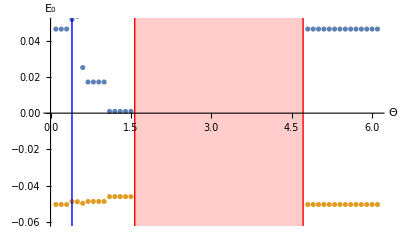

```mathematica
ListPlot[{ExtractRe@thetaTable, ExtractIm@thetaTable},
AxesLabel->{"Θ","E_0"},
PlotRange->{{0,6.1},{-0.06,0.05}},
Epilog->{
{Blue, Line[{{0.4,-100},{0.4,100}}]},
 {Red,Line[{{Pi/2,-100},{Pi/2,100}}]},
{Red,Line[{{3Pi/2,-100},{3Pi/2,100}}]}},
Prolog->{Opacity[0.2,Red],Rectangle[{Pi/2,-1*^4},{3 Pi/2,1*^4}]}
]
```

Because we set ℏ = ⅈ, the poles effectively rotate by -Pi/2.

```mathematica
thetaLine[Θ_] :=Table[r Exp[I Θ], {r,0,20, 1}]
```

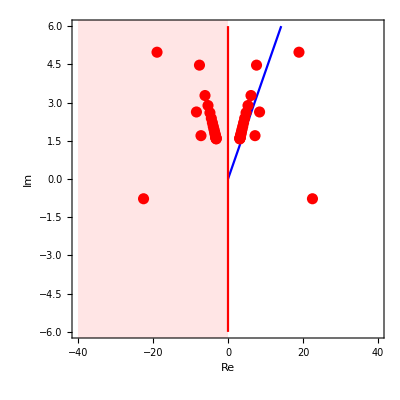

```mathematica
p1=ListLinePlot[{Re[#],Im[#]}&/@(thetaLine[0.4]),AxesOrigin->{0,0},ImagePadding->50,AspectRatio->1,Frame->True,FrameLabel->{{Im,None},{Re,"complex plane"}},PlotStyle->Directive[Blue,PointSize[.02]],
PlotRange->{{-40, 40},{-6, 6}},
Prolog->{Opacity[0.1,Red],Rectangle[{-40,-1*^4},{0,1*^4}]}];
p1b = ListLinePlot[{Re[#],Im[#]}&/@(thetaLine[Pi/2]),AxesOrigin->{0,0},ImagePadding->50,AspectRatio->1,Frame->True,FrameLabel->{{Im,None},{Re,"complex plane"}},PlotStyle->Directive[Red,PointSize[.02]],
PlotRange->{{-40, 40},{-6, 6}}];
p2 = ListLinePlot[{Re[#],Im[#]}&/@(thetaLine[3 Pi/2]),AxesOrigin->{0,0}, ImagePadding->50,AspectRatio->1,Frame->True,FrameLabel->{{Im,None},{Re,"complex plane"}},PlotStyle->Directive[Red,PointSize[.02]],
PlotRange->{{-40, 40},{-6, 6}}];
p3 = ListPlot[{Re[#],Im[#]}&/@(Flatten@(polesTable Exp[-I Pi/2])),AxesOrigin->{0,0},ImagePadding->50,AspectRatio->1,Frame->True,FrameLabel->{{Im,None},{Re,"complex plane"}},PlotStyle->Directive[Red,PointSize[.02]],
PlotRange->{{-40, 40},{-6, 6}}];
Show[p1,p1b, p2,p3]
```

We can see that when we cross the poles (branch cut there I guess), there is a jump in the energy.
Once we cross π/2 the Laplace transform diverges.
Once we cross (3π)/2 the Laplace transform starts converging again.